```mathematica
NumOfAvs = {6,
12,
16,
27,
30,
36,
45,
54,
63,
72,
81};
```

```mathematica
MaxTime = {0.5003312,
2.000264,
3.200372,
5.0186612,
7.00015,
10,
16.0013,
18.5001,
24.0017,
30.002,
35.002
};
```

```mathematica
m= {NumOfAvs,MaxTime};
```

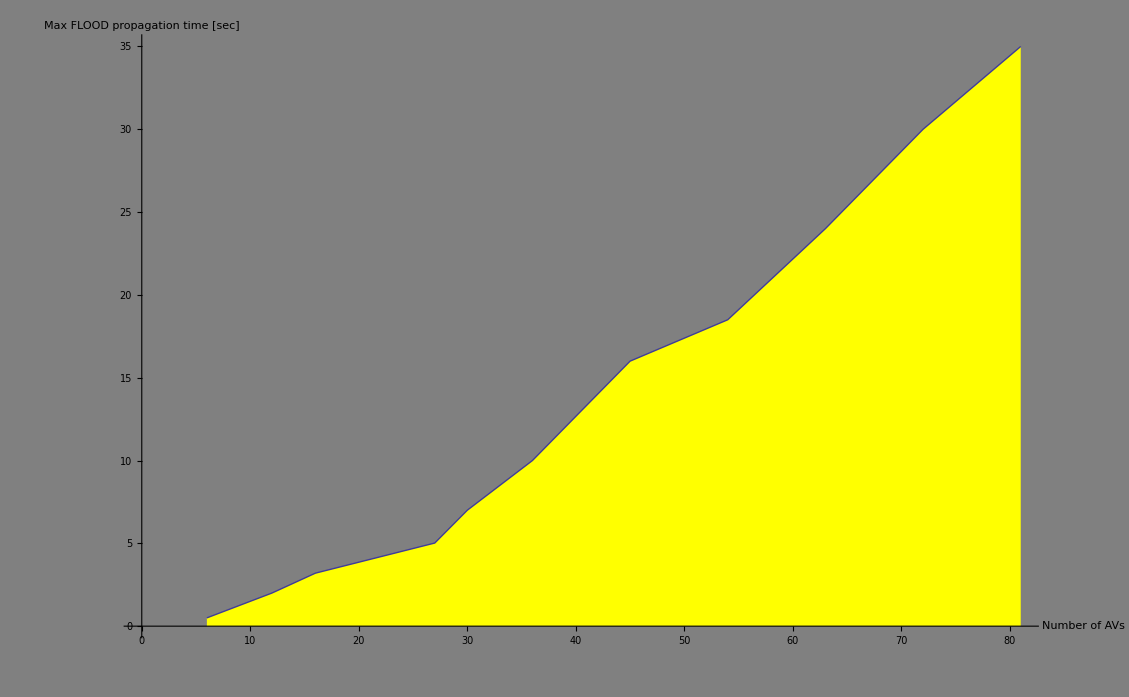

```mathematica
ListLinePlot[Transpose[m],AxesLabel->{"Number of AVs","Max FLOOD propagation time [sec]"},FillingStyle->Yellow, Filling->Bottom, Background-> Gray, LabelStyle->{Yellow,18}]
```

```mathematica
NumOfPackets = {44.3,
56.3,
69,
88.3,92,
100.3,
129.3,
186.3,
209.3,
222.3,
247.66
};
```

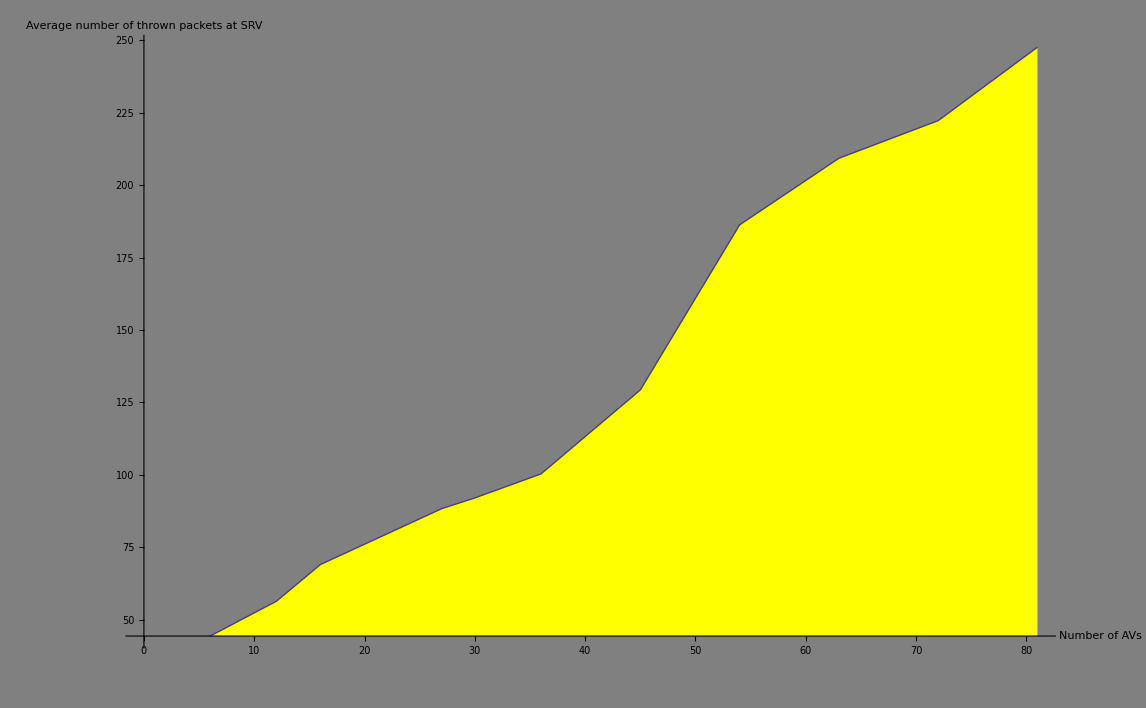

```mathematica
ListLinePlot[Transpose[{NumOfAvs,NumOfPackets}],AxesLabel->{"Number of AVs","Average number of thrown packets at SRV"},FillingStyle->Yellow, Filling->Bottom, Background-> Gray, LabelStyle->{Yellow,18}]
```

```mathematica
NumOfCollisions = {8,
21,
23,
50,52,
60,
104,
128,
177,
190,
234
};
```

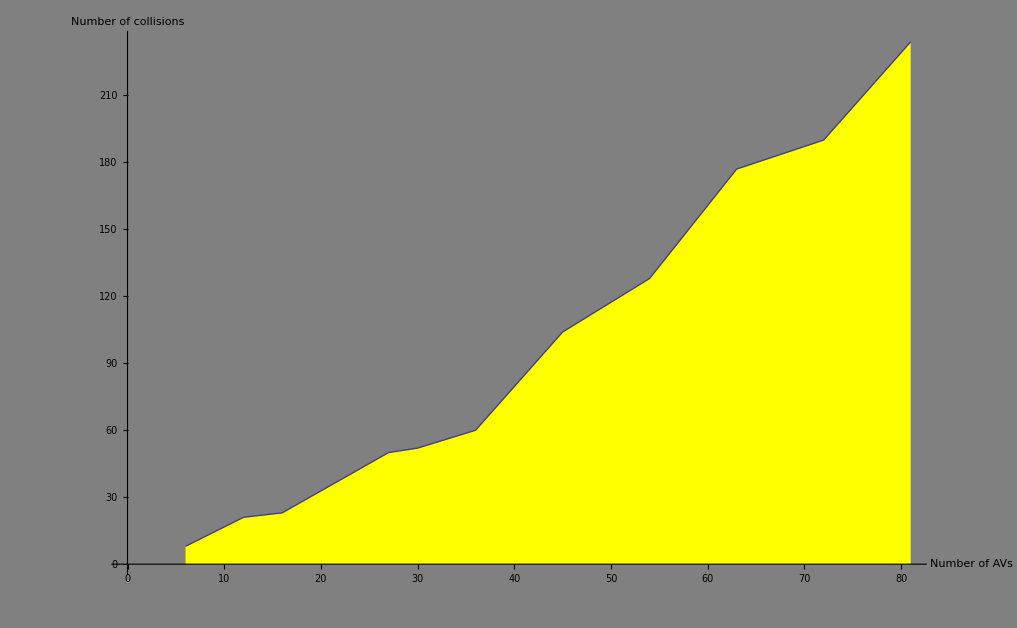

```mathematica
ListLinePlot[Transpose[{NumOfAvs,NumOfCollisions}],AxesLabel->{"Number of AVs","Number of collisions"},FillingStyle->Yellow, Filling->Bottom, Background-> Gray, LabelStyle->{Yellow,18}]
```

```mathematica
NumOfAvs1 = {3,
6,
9,
12,
15,
18,
21,
24,
27,
30,
33,
36,
39
};
```

```mathematica
NumOfAvs2 = {5,
10,
15,
20,
25,
30,
35,
40
};
```

```mathematica
FLR1 = {12.3,
7.333333333,
10,
10.6,
6.133333333,
9.333333333,
7.2,
9.3,
9.2,
7.166666667,
13.27272727,
8.3,
9
};
```

{12.3,7.33333,10,10.6,6.13333,9.33333,7.2,9.3,9.2,7.16667,13.2727,8.3,9}

```mathematica
FLR2 = {0,0,0,0,10,1600,3200,4800};
```

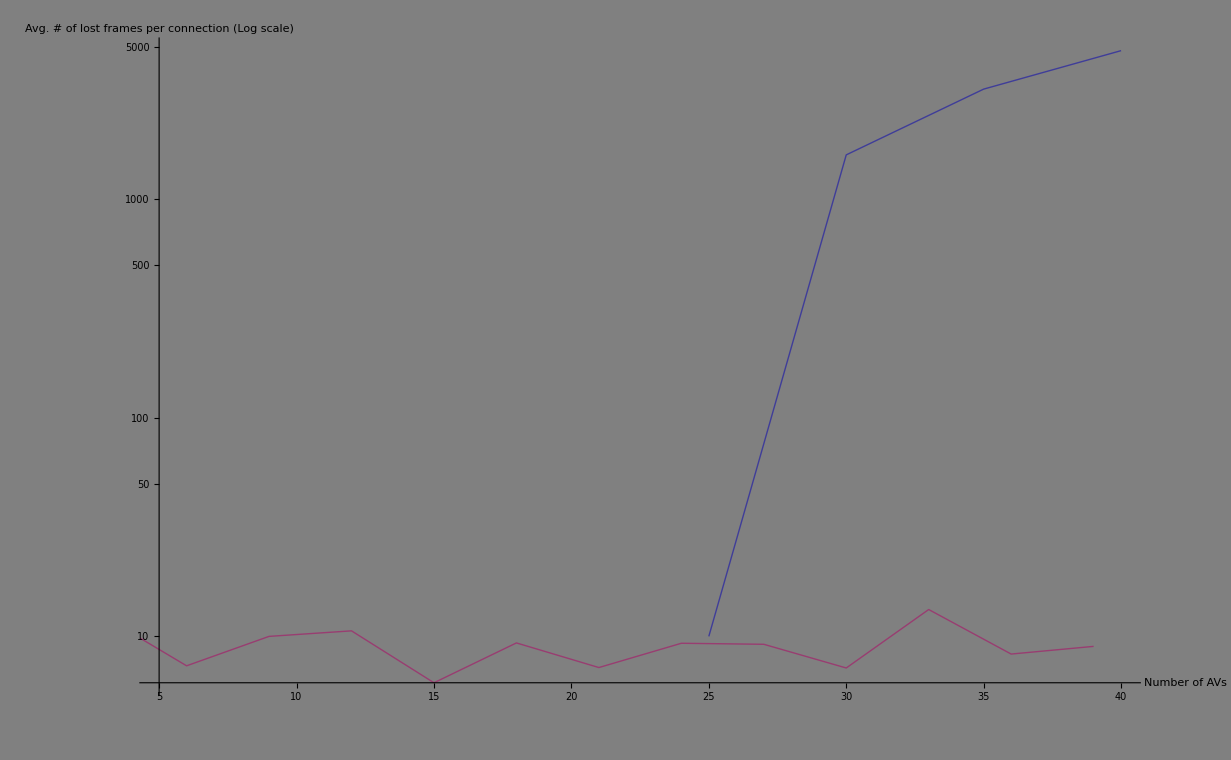

```mathematica
ListLogPlot[{Transpose[{NumOfAvs2,FLR2}],Transpose[{NumOfAvs1,FLR1}]},AxesLabel->{"Number of AVs","Avg. # of lost frames per connection (Log scale)"}, Background-> Gray, LabelStyle->{Yellow,18},PlotRange->
{{5,40},{0,10000}},Joined->True,PlotStyle->{Thick}]
```